# Approximate Quasisymmetry

## Input Parameters

```mathematica
R0=1;sigma0=0;NFP=2;
(*Number of Axis Fourier Coefficients*)
naxR=2;naxZ=naxR;
(*psi initial = psi31,psi32,psi33,psi34,sigma,F0*)
psiinit[t_]={0.01Cos[NFP t],0.01Sin[NFP t],0.01Cos[NFP t],0.01Sin[NFP t],0.01 Cos[NFP t],0.1};
```

## Axis Functions

```mathematica
R[x_]=R0+Sum[eR[n] Cos[n NFP x],{n,1,naxR}];
Z[x_]=Sum[eZ[n] Sin[n NFP x],{n,1,naxZ}];
closedCurve[x_]={R[x]Cos[x],R[x]Sin[x],Z[x]};
 curvFunc1[x_]=Chop[ComplexExpand[Norm[Cross[closedCurve'[x], closedCurve''[x]]]]/ComplexExpand[Norm[closedCurve'[x]]^3],10^-6];
torsFunc1[x_]=Chop[Dot[Cross[closedCurve'[x], closedCurve''[x]], closedCurve'''[x]]/ComplexExpand[Norm[Cross[closedCurve'[x], closedCurve''[x]]]]^2,10^-6];
sprimeFunc1[x_]=Chop[ComplexExpand[Norm[closedCurve'[x]]],10^-6]//Quiet;
```

```mathematica
optsComp={Table[eR[n]->er[[n]],{n,1,naxR}],Table[eZ[n]->ez[[n]],{n,1,naxZ}]}//Flatten//Quiet;
{curvFunc[phi_,er_,ez_],curvFuncp[phi_,er_,ez_],curvFuncpp[phi_,er_,ez_],curvFuncppp[phi_,er_,ez_]}={curvFunc1[phi],D[curvFunc1[phi],phi]/sprimeFunc1[phi],D[D[curvFunc1[phi],phi]/sprimeFunc1[phi],phi] 1/sprimeFunc1[phi],D[D[D[curvFunc1[phi],phi]/sprimeFunc1[phi],phi] 1/sprimeFunc1[phi],phi] 1/sprimeFunc1[phi]}/.optsComp//Quiet;
{torsFunc[phi_,er_,ez_],torsFuncp[phi_,er_,ez_],torsFuncpp[phi_,er_,ez_]}={torsFunc1[phi],D[torsFunc1[phi],phi]/sprimeFunc1[phi],D[D[torsFunc1[phi],phi]/sprimeFunc1[phi],phi] 1/sprimeFunc1[phi]}/.optsComp//Quiet;
sprimeFunc[phi_,er_,ez_]=sprimeFunc1[phi]/.optsComp//Quiet;
```

## Set of Equations

```mathematica
(*σ'[s]-sigmap[s]=0*)
sigmap[s_]=Flatten@(-(F0 ηb^4)/k[s]^4-F0 (1+σ[s]^2)-(2 ηb^2 α'[s])/k[s]^2);
(*psi'-psiMatA[s]psi[s]-psiMatB[s]=0*)
psiMatA[s_]=({{-6 F0 σ[s]+(2 k'[s])/k[s], (4 F0 ηb^2)/k[s]^2+3 α'[s], (3 k'[s])/k[s], (3 (F0 ηb^4+F0 k[s]^4 (1+σ[s]^2)+ηb^2 k[s]^2 α'[s]))/(ηb^2 k[s]^2)}, {(2 F0 ηb^2)/k[s]^2+(F0 ηb^4+F0 k[s]^4 (1+σ[s]^2)+ηb^2 k[s]^2 α'[s])/(ηb^2 k[s]^2), 4 F0 σ[s]-(2 k'[s])/k[s], -(3 (F0 ηb^4+F0 k[s]^4 (1+σ[s]^2)+ηb^2 k[s]^2 α'[s]))/(ηb^2 k[s]^2), (3 k'[s])/k[s]}, {-2 F0 σ[s]+k'[s]/k[s], -(2 F0 ηb^2)/k[s]^2-α'[s], 0, (3 (F0 ηb^4+F0 k[s]^4 (1+σ[s]^2)+ηb^2 k[s]^2 α'[s]))/(ηb^2 k[s]^2)}, {(2 F0 ηb^2)/k[s]^2+(F0 ηb^4+F0 k[s]^4 (1+σ[s]^2)+ηb^2 k[s]^2 α'[s])/(ηb^2 k[s]^2), -2 F0 σ[s]+k'[s]/k[s], -(3 (F0 ηb^4+F0 k[s]^4 (1+σ[s]^2)+ηb^2 k[s]^2 α'[s]))/(ηb^2 k[s]^2), 0}});
psiMatB[s_]=Flatten@({{(48 F0^3 ηb^10 k[s] σ[s]+8 F0^2 ηb^10 k'[s]+3 k[s]^10 (1+σ[s]^2) k'[s] (-ηb^2+4 F0 (1+σ[s]^2) α'[s])+4 k[s]^2 (3 ηb^6 k'[s]^3+7 F0 ηb^8 k'[s] α'[s])+3 F0 k[s]^11 (1+σ[s]^2) (5 ηb^2 σ[s]-8 F0 (σ[s]+σ[s]^3) α'[s]+2 (1+σ[s]^2) α''[s])+8 k[s]^5 (ηb^4 σ[s] (4 F0^3 ηb^2 (3+4 σ[s]^2)-k'[s]^2 α'[s]+10 F0 ηb^2 α'[s]^2)-2 ηb^6 α'[s] α''[s])+2 ηb^2 k[s]^9 (8 F0^3 σ[s] (3+8 σ[s]^2+5 σ[s]^4)+3 ηb^2 σ[s] α'[s]-16 F0 (σ[s]+σ[s]^3) α'[s]^2+8 (1+σ[s]^2) α'[s] α''[s])+2 ηb^6 k[s]^3 (2 F0 σ[s] (7 k'[s]^2+34 F0 ηb^2 α'[s])-5 (k'[s] k''[s]+F0 ηb^2 α''[s]))+ηb^2 k[s]^6 (-12 (1+σ[s]^2) k'[s]^3+16 ηb^2 σ[s] α'[s] k''[s]+ηb^2 k'[s] (ηb^2-8 F0 (5+9 σ[s]^2) α'[s]+8 σ[s] α''[s]))-2 ηb^2 k[s]^8 (1+σ[s]^2) (2 k'[s] (2 F0^2 (1+7 σ[s]^2)-α'[s]^2)-2 F0 σ[s] k''[s]+Derivative[3][k][s])+2 ηb^6 k[s]^4 (-2 k'[s] (4 F0^2 σ[s]^2+α'[s]^2)-2 F0 σ[s] k''[s]+Derivative[3][k][s])+ηb^2 k[s]^7 (4 F0 σ[s]^3 (5 k'[s]^2+36 F0 ηb^2 α'[s])+10 k'[s] k''[s]+4 F0 ηb^2 α''[s]+2 σ[s]^2 (5 k'[s] k''[s]-6 F0 ηb^2 α''[s])+σ[s] (17 F0 ηb^4+20 F0 k'[s]^2+4 ηb^2 (28 F0^2 α'[s]-2 α'[s]^3+Derivative[3][α][s]))))/(4 ηb^4 k[s]^8)}, {(8 F0^3 ηb^8)/k[s]^9+(2 F0 ηb^4 (3 k'[s]^2+8 F0 ηb^2 α'[s]))/k[s]^7-(F0 k[s]^3 (1+σ[s]^2)^2 (4 F0^2 (1+2 σ[s]^2)-α'[s]^2))/ηb^4+(4 F0^3 ηb^4 (1+4 σ[s]^2)-ηb^2 k'[s]^2 α'[s]+7 F0 ηb^4 α'[s]^2)/k[s]^5+(F0 k[s]^2 (1+σ[s]^2)^2 (4 F0 σ[s] k'[s]-k''[s]))/ηb^4-(F0 ηb^4 (8 F0 σ[s] k'[s]+k''[s]))/k[s]^6+(ηb^2 σ[s] k'[s]+10 F0 σ[s] k'[s] α'[s]+10 F0 σ[s]^3 k'[s] α'[s]-2 α'[s] k''[s]-2 σ[s]^2 α'[s] k''[s]-(1+σ[s]^2) k'[s] α''[s])/ηb^2+(-8 F0^3+(-ηb^2/2+k'[s]^2/ηb^2) α'[s]-8 F0 α'[s]^2+σ[s]^2 (-8 F0^3+(k'[s]^2 α'[s])/ηb^2-20 F0 α'[s]^2)+8 σ[s] α'[s] α''[s])/k[s]+(-6 σ[s] (k'[s]^3+3 F0 ηb^2 k'[s] α'[s])+ηb^2 (2 α'[s] k''[s]+k'[s] α''[s]))/k[s]^4+(-12 F0^2 σ[s]^3 k'[s]+2 F0 k''[s]-σ[s] (k'[s] (4 F0^2-2 α'[s]^2)+Derivative[3][k][s]))/k[s]^2-(k[s] (2 F0 ηb^2+4 F0 ηb^2 σ[s]^2+24 F0^2 α'[s]+80 F0^2 σ[s]^2 α'[s]+56 F0^2 σ[s]^4 α'[s]-2 α'[s]^3-2 σ[s]^2 α'[s]^3-10 F0 (σ[s]+σ[s]^3) α''[s]+(1+σ[s]^2) Derivative[3][α][s]))/(2 ηb^2)+(4 F0 (-3+2 σ[s]^2) k'[s]^2+10 σ[s] k'[s] k''[s]+ηb^2 (-8 F0^2 (1+σ[s]^2) α'[s]-2 α'[s]^3-3 F0 (ηb^2-2 σ[s] α''[s])+Derivative[3][α][s]))/(2 k[s]^3)}, {(16 F0^3 ηb^10 k[s] σ[s]-8 F0^2 ηb^10 k'[s]+k[s]^10 (1+σ[s]^2) k'[s] (ηb^2+12 F0 (1+σ[s]^2) α'[s])+ηb^2 k[s]^6 k'[s] (-ηb^4-12 (1+σ[s]^2) k'[s]^2-16 F0 ηb^2 (1+σ[s]^2) α'[s])-4 k[s]^2 (3 ηb^6 k'[s]^3+7 F0 ηb^8 k'[s] α'[s])+3 F0 k[s]^11 (1+σ[s]^2) (ηb^2 σ[s]-8 F0 (σ[s]+σ[s]^3) α'[s]+2 (1+σ[s]^2) α''[s])+8 ηb^6 k[s]^5 (4 F0^3 σ[s]^3+σ[s] (4 F0^3-3 F0 α'[s]^2)+2 α'[s] α''[s])+2 ηb^2 k[s]^9 (8 F0^3 σ[s] (1+σ[s]^2)^2+ηb^2 σ[s] α'[s]-12 F0 (σ[s]+σ[s]^3) α'[s]^2+8 (1+σ[s]^2) α'[s] α''[s])+2 ηb^6 k[s]^3 (2 F0 σ[s] (5 k'[s]^2-2 F0 ηb^2 α'[s])+5 (k'[s] k''[s]+F0 ηb^2 α''[s]))+ηb^2 k[s]^7 (F0 σ[s] (7 ηb^4+20 k'[s]^2-32 F0 ηb^2 α'[s])+4 F0 σ[s]^3 (5 k'[s]^2-8 F0 ηb^2 α'[s])+2 (5 k'[s] k''[s]+8 F0 ηb^2 α''[s])+2 σ[s]^2 (5 k'[s] k''[s]+8 F0 ηb^2 α''[s]))-2 ηb^6 k[s]^4 (2 k'[s] (4 F0^2 (1+2 σ[s]^2)-α'[s]^2)+2 F0 σ[s] k''[s]+Derivative[3][k][s])-2 ηb^2 k[s]^8 (1+σ[s]^2) (2 k'[s] (2 F0^2 (1+3 σ[s]^2)-α'[s]^2)+2 F0 σ[s] k''[s]+Derivative[3][k][s]))/(4 ηb^4 k[s]^8)}, {-(8 F0^3 ηb^8)/k[s]^9-(-16 F0^2 ηb^4 k[s]^5 σ[s] (1+σ[s]^2) k'[s]+4 F0 ηb^8 (3 k'[s]^2+8 F0 ηb^2 α'[s])+2 F0 k[s]^10 (1+σ[s]^2)^2 (4 F0^2 (1+2 σ[s]^2)-α'[s]^2)+2 ηb^6 k[s]^2 (4 F0^3 ηb^2 (5+6 σ[s]^2)-k'[s]^2 α'[s]+7 F0 ηb^2 α'[s]^2)+ηb^2 k[s]^6 (16 F0^3 ηb^2 (2+5 σ[s]^2+3 σ[s]^4)+(ηb^4-2 (1+σ[s]^2) k'[s]^2) α'[s]+12 F0 ηb^2 (1+σ[s]^2) α'[s]^2)-2 F0 k[s]^9 (1+σ[s]^2)^2 (4 F0 σ[s] k'[s]-k''[s])-2 F0 ηb^8 k[s] (4 F0 σ[s] k'[s]+k''[s])+2 ηb^6 k[s]^3 (-4 F0 σ[s] k'[s] α'[s]+2 α'[s] k''[s]+k'[s] α''[s])+ηb^2 k[s]^7 (ηb^2 σ[s] k'[s]-8 F0 σ[s] k'[s] α'[s]-8 F0 σ[s]^3 k'[s] α'[s]+4 α'[s] k''[s]+4 σ[s]^2 α'[s] k''[s]+2 (1+σ[s]^2) k'[s] α''[s])+ηb^2 k[s]^8 (2 F0 ηb^2+24 F0^2 α'[s]+32 F0^2 σ[s]^4 α'[s]-2 α'[s]^3-4 F0 σ[s] α''[s]-4 F0 σ[s]^3 α''[s]+Derivative[3][α][s]+σ[s]^2 (F0 ηb^2+56 F0^2 α'[s]-2 α'[s]^3+Derivative[3][α][s]))+ηb^4 k[s]^4 (12 F0 (1+σ[s]^2) k'[s]^2+ηb^2 (8 F0^2 (7+8 σ[s]^2) α'[s]-2 α'[s]^3+F0 (3 ηb^2-4 σ[s] α''[s])+Derivative[3][α][s])))/(2 ηb^4 k[s]^7)}});
(*psi2[s]-psi32[s]=0*)
psi32[s_]=1/(B0 π)1/(4 F0 ηb^2 k[s]^6)B0 π (16 F0^3 ηb^6 k[s] σ[s]+8 F0^2 ηb^6 k'[s]+4 ηb^2 k[s]^2 k'[s] (k'[s]^2+F0 ηb^2 α'[s])-k[s]^6 k'[s] (ηb^2+4 F0 (1+σ[s]^2) α'[s])+4 F0 ηb^2 k[s]^4 (-2 F0 (1+σ[s]^2) k'[s]+σ[s] k''[s])+2 ηb^2 k[s]^3 (2 F0 σ[s] (-k'[s]^2+6 F0 ηb^2 α'[s])-2 k'[s] k''[s]-3 F0 ηb^2 α''[s])+F0 k[s]^7 (8 F0 σ[s]^3 α'[s]+σ[s] (ηb^2+8 F0 α'[s])-2 α''[s]-2 σ[s]^2 α''[s])+4 ηb^2 k[s]^5 (4 F0^3 σ[s]^3+2 F0 σ[s] (2 F0^2+α'[s]^2)-α'[s] α''[s]));
```

## Compiled Functions

```mathematica
erT=Table[eR[i],{i,1,naxR}];ezT=Table[eZ[i],{i,1,naxZ}];
opts1={k[phi]->curvFunc[phi,er,ez],k'[phi]->curvFuncp[phi,er,ez],k''[phi]->curvFuncpp[phi,er,ez],k'''[phi]->curvFuncppp[phi,er,ez],α'[phi]->torsFunc[phi,er,ez],α''[phi]->torsFuncp[phi,er,ez],α'''[phi]->torsFuncpp[phi,er,ez],σ[phi]->psi[5],F0->psi[6],ηb->etabb}//Quiet;
optsCT3={Table[psi[i]->psii[[i]],{i,1,6}],etabb->etabbb}//Quiet//Flatten;
fpsi3=Compile[{{phi,_Real},{er,_Real,1},{ez,_Real,1},{psii,_Real,1},{etabbb,_Real}},Evaluate[(-sprimeFunc[phi,er,ez](psiMatA[phi].{psi[1],psi[2],psi[3],psi[4]}+psiMatB[phi]))/.opts1/.optsCT3],CompilationTarget->"C",Parallelization->True,RuntimeAttributes->{Listable},RuntimeOptions->"Speed"]//Quiet;
fsigma=Compile[{{phi,_Real},{er,_Real,1},{ez,_Real,1},{psii,_Real,1},{etabbb,_Real}},Evaluate[(-sprimeFunc[phi,er,ez]sigmap[phi])/.opts1/.optsCT3],CompilationTarget->"C",Parallelization->True,RuntimeAttributes->{Listable},RuntimeOptions->"Speed"]//Quiet;
dfpsi3=Compile[{{phi,_Real},{er,_Real,1},{ez,_Real,1},{psii,_Real,1},{etabbb,_Real}},Evaluate[-sprimeFunc[phi,er,ez](psiMatA[phi])/.opts1/.optsCT3],CompilationTarget->"C",Parallelization->True,RuntimeAttributes->{Listable},RuntimeOptions->"Speed"]//Quiet;
dfsigma=Compile[{{phi,_Real},{er,_Real,1},{ez,_Real,1},{psii,_Real,1},{etabbb,_Real}},Evaluate[-sprimeFunc[phi,er,ez](D[sigmap[phi],σ[phi]])/.opts1/.optsCT3],CompilationTarget->"C",Parallelization->True,RuntimeAttributes->{Listable},RuntimeOptions->"Speed"]//Quiet;
dfdF0=Compile[{{phi,_Real},{er,_Real,1},{ez,_Real,1},{psii,_Real,1},{etabbb,_Real}},Evaluate[-sprimeFunc[phi,er,ez](D[sigmap[phi],F0])/.opts1/.optsCT3],CompilationTarget->"C",Parallelization->True,RuntimeAttributes->{Listable},RuntimeOptions->"Speed"]//Quiet;
fpsi2=Compile[{{phi,_Real},{er,_Real,1},{ez,_Real,1},{psii,_Real,1},{etabbb,_Real}},Evaluate[(psi[2]-psi32[phi])/.opts1/.optsCT3],CompilationTarget->"C",Parallelization->True,RuntimeAttributes->{Listable},RuntimeOptions->"Speed"]//Quiet;
```

## Residual and Jacobian Matrices

## Sigma

```mathematica
Clear[qsresidualsigma];
qsresidualsigma[Dmat_,psii_,er_,ez_,etab_,ns_,sigma0_]:=Module[
{delta=(2 π)/ns },
fsigmaMat=Table[fsigma[delta i,er,ez,psii[[i]],etab],{i,1,ns}];
dfsigmaMat=Table[dfsigma[delta i,er,ez,psii[[i]],etab],{i,1,ns}];
dfdF0Mat=Table[dfdF0[delta i,er,ez,psii[[i]],etab],{i,1,ns}];
f1Mat={
Dmat.psii[[All,5]]+fsigmaMat[[All]],
psii[[ns,5]]-sigma0
}//Flatten;
myArrayFlatten=Flatten/@Flatten[#,{{1,3}}]&;
Jacf1Mat=myArrayFlatten@{
{Dmat+DiagonalMatrix[dfsigmaMat],dfdF0Mat}
};
Jacf1Mat=Append[Jacf1Mat,{ConstantArray[0, ns-1],1,0}//Flatten];
{f1Mat,Jacf1Mat}
];
solveSigma[Dmat_,nIts_,tol_,nLineS_,psiA_,er_,ez_,etab_,ns_,sigma0_]:=Module[
{deltaold=0,delta=(2 π)/ns },
psii=psiA;
For[i=1,i≤nIts,i++,
{f1,Jacf1}=qsresidualsigma[Dmat,psii,er,ez,etab,ns,sigma0];
deltay=-LinearSolve[Jacf1,f1]//Quiet;
res[i]=Norm[deltay];
If[(Abs[Norm[deltay]-Norm[deltaold]])/√ns<tol,Break[]];
For[j=1,j<nLineS,j++,
psiAtemp=psii;psiAtemp[[All,5]]=psiAtemp[[All,5]]+deltay[[1;;ns]];psiAtemp[[All,6]]=psiAtemp[[All,6]]+deltay[[ns+1]];
{f2,Jacf2}=qsresidualsigma[Dmat,psiAtemp,er,ez,etab,ns,sigma0];
If[Abs[Norm[f2]]<Abs[Norm[f1]],Break[],deltay=deltay/2];
];
psii=psiAtemp;
deltaold=deltay;
];
psii
]
```

## Psi3

```mathematica
Clear[qsresidualpsi3];
qsresidualpsi3[Dmat_,psii_,er_,ez_,etab_,ns_,sigma0_]:=Module[
{delta=(2 π)/ns },
fpsi3Mat=Table[fpsi3[delta i,er,ez,psii[[i]],etab],{i,1,ns}];
dfpsi3Mat=Table[dfpsi3[delta i,er,ez,psii[[i]],etab],{i,1,ns}];
f1Mat={
Dmat.psii[[All,1]]+fpsi3Mat[[All,1]],
Dmat.psii[[All,2]]+fpsi3Mat[[All,2]],
Dmat.psii[[All,3]]+fpsi3Mat[[All,3]],
Dmat.psii[[All,4]]+fpsi3Mat[[All,4]]
}//Flatten;
zeroarray=DiagonalMatrix[ConstantArray[0,ns]];
myArrayFlatten=Flatten/@Flatten[#,{{1,3}}]&;
Jacf1Mat=myArrayFlatten@{
{Dmat+DiagonalMatrix[dfpsi3Mat[[All,1,1]]],DiagonalMatrix[dfpsi3Mat[[All,1,2]]],DiagonalMatrix[dfpsi3Mat[[All,1,3]]],DiagonalMatrix[dfpsi3Mat[[All,1,4]]]},
{DiagonalMatrix[dfpsi3Mat[[All,2,1]]],Dmat+DiagonalMatrix[dfpsi3Mat[[All,2,2]]],DiagonalMatrix[dfpsi3Mat[[All,2,3]]],DiagonalMatrix[dfpsi3Mat[[All,2,4]]]},
{DiagonalMatrix[dfpsi3Mat[[All,3,1]]],DiagonalMatrix[dfpsi3Mat[[All,3,2]]],Dmat+DiagonalMatrix[dfpsi3Mat[[All,3,3]]],DiagonalMatrix[dfpsi3Mat[[All,3,4]]]},
{DiagonalMatrix[dfpsi3Mat[[All,4,1]]],DiagonalMatrix[dfpsi3Mat[[All,4,2]]],DiagonalMatrix[dfpsi3Mat[[All,4,3]]],Dmat+DiagonalMatrix[dfpsi3Mat[[All,4,4]]]}
};
{f1Mat,Jacf1Mat}
];
solvepsi3[Dmat_,nIts_,tol_,nLineS_,psiA_,er_,ez_,etab_,ns_,sigma0_]:=Module[
{deltaold=0,delta=(2 π)/ns },
psii=psiA;
For[i=1,i≤nIts,i++,
{f1,Jacf1}=qsresidualpsi3[Dmat,psii,er,ez,etab,ns,sigma0];
deltay=-LinearSolve[Jacf1,f1]//Quiet;
res[i]=Norm[deltay];
If[(Abs[Norm[deltay]-Norm[deltaold]])/√ns<tol,Break[]];
For[j=1,j<nLineS,j++,
psiAtemp=psii;psiAtemp[[All,1]]=psiAtemp[[All,1]]+deltay[[1;;ns]];psiAtemp[[All,2]]=psiAtemp[[All,2]]+deltay[[ns+1;;2ns]];
psiAtemp[[All,3]]=psiAtemp[[All,3]]+deltay[[2ns+1;;3ns]];psiAtemp[[All,4]]=psiAtemp[[All,4]]+deltay[[3ns+1;;4ns]];
{f2,Jacf2}=qsresidualpsi3[Dmat,psiAtemp,er,ez,etab,ns,sigma0];
If[Abs[Norm[f2]]<Abs[Norm[f1]],Break[],deltay=deltay/2];
];
psii=psiAtemp;
deltaold=deltay;
];
psii
]
```

## Objective Function

```mathematica
Clear[objFuncpsi3];
objFuncpsi3[etab_,er0_,ez0_,nIts_,tol_,nLineS_,psiinit_,ns_,sigma0_]:=
Module[{delta=(2 Pi)/ns},
psii=Table[psiinit[delta i],{i,1,ns}];
(*Derivative Matrix*)
column1=Prepend[ Table[ 0.5 (-1)^n Cot[n/2 delta],{n,1,ns-1}],0];
column2=RotateRight[Reverse[column1]];
Dmat=ToeplitzMatrix[column1,column2];
(*Solve Sigma*)
psisol1=solveSigma[Dmat,nIts,tol,nLineS,psii,er0,ez0,etab,ns,sigma0];
(*Solve Psi3*)
psisol2=solvepsi3[Dmat,nIts,tol,nLineS,psisol1,er0,ez0,etab,ns,sigma0];
(*psi2 Constraint*)
residpsi2=Table[fpsi2[delta i,er0,ez0,psisol2[[i]],etab],{i,1,ns}];
{Norm[residpsi2]+Norm[psisol2[[All,1;;4]]]-Norm[psisol2[[1,6]]],psisol2,residpsi2}
];
```

## Optimization

```mathematica
ns=120;nIts=18;nLineS=5;maxiterations=50;tol=10^-6;
etabmin=0.4;etabmax=1.7;eR1min=0.09;eR1max=0.2;eZ1min=0.01;eZ1max=0.2;
eR2min=-0.08;eR2max=0.08;eZ2min=eR2min;eZ2max=eR2max;
eR3min=-0.008;eR3max=0.008;eZ3min=eR3min;eZ3max=eR3max;eR4min=-0.001;eR4max=0.001;eZ4min=eR4min;eZ4max=eR4max;
```

## Definitions for Run

```mathematica
eRT=ToExpression[Table["eR"<>ToString[i],{i,1,naxR}]];
eZT=ToExpression[Table["eZ"<>ToString[i],{i,1,naxR}]];
eRZT=Flatten[Append[Append[{{{etabb,etabmin,etabmax}}},ToExpression[Table[{"eR"<>ToString[i],"eR"<>ToString[i]<>"min","eR"<>ToString[i]<>"max"},{i,1,naxR}]]],ToExpression[Table[{"eZ"<>ToString[i],"eZ"<>ToString[i]<>"min","eZ"<>ToString[i]<>"max"},{i,1,naxR}]]],1];
consts="etabmin<etabb<etabmax&&";
Do[consts=consts<>"eR"<>ToString[i]<>"min"<>"<eR"<>ToString[i]<>"<"<>"eR"<>ToString[i]<>"max"<>"&&",{i,1,naxR}];
Do[consts=consts<>"eZ"<>ToString[i]<>"min"<>"<eZ"<>ToString[i]<>"<"<>"eZ"<>ToString[i]<>"max"<>"&&",{i,1,naxZ}];
consts=ToExpression[StringDrop[consts,-2]];
erzs="etab";Do[erzs=erzs<>", eR"<>ToString[i],{i,1,naxR}];Do[erzs=erzs<>", eZ"<>ToString[i],{i,1,naxZ}];
```

## Run Optimization Procedure

```mathematica
varstemp={};OutputFile="/Users/rogeriojorge/Dropbox/senac/quasisymmetry/HighOrderQSmath.txt";
Export[OutputFile,erzs<>"\n"];ii=0;
(*Dynamic@If[Length@varstemp>3,ListPlot[Transpose@varstemp,PlotRange->{Automatic,{-0.2,0.2}},GridLines->{{Length@varstemp},{}},PlotLegends->{OverBar["η"]/8,"eR_1","10 eR_2","10 eR_3","eZ_1","10 eZ_2","10 eZ_3"},ImageSize->1100,PlotStyle->{PointSize[.005]}]]*)
{etabsol,eRsol,eZsol}={etabb,eRT,eZT}/.NMinimize[
{Hold[objFuncpsi3[etabb,eRT,eZT,nIts,tol,nLineS,psiinit,ns,sigma0][[1]]],consts},
eRZT,
AccuracyGoal->3,PrecisionGoal->3,WorkingPrecision->8,MaxIterations->maxiterations(*,Method->{"DifferentialEvolution","ScalingFactor"->5}*)
,(*EvaluationMonitor:>AppendTo[varstemp,{etabb/8,eR1,10  eR2,10 eR3, eZ1,10eZ2,10eZ3}],*)
StepMonitor:>{ii++,its="Iteration "<>ToString@ii<>" -> "<>ToString[etabb],Do[its=its<>", "<>ToString[ToExpression["eR"<>ToString[i]]],{i,1,naxR}],Do[its=its<>", "<>ToString[ToExpression["eZ"<>ToString[i]]],{i,1,naxZ}],PutAppend[its,OutputFile];{etabsol,eRsol,eZsol}={etabb,ToExpression[eRT],ToExpression[eZT]}}
][[2]];
PutAppend["Solution with objective function = "<>ToString@(objFuncpsi3[etabsol,eRsol,eZsol,nIts,tol,nLineS,psiinit,ns,sigma0][[1]])<>" -> "<>ToString@etabsol<>", "<>ToString@eRsol<>", "<>ToString@eZsol,OutputFile];
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 50 iterations.

## New Solution

```mathematica
(*etabsol=1.51013;
eRsol={0.360407,-0.0669714,0.00460894,-0.000223451};
eZsol={0.399998,-0.0693047,0.00480132,-0.000227014};*)
(*etabsol=0.712883;eRsol={0.100555,0.00512315,0.000298938,-8.18719 10^-6};eZsol={0.100972,0.00587665,0.000344878,-0.0000119423};*)
solfin=objFuncpsi3[etabsol,eRsol,eZsol,30,10^-11,10,psiinit,500,sigma0];
(*ListLinePlot[solfin[[3,All]],PlotRange->All]*)
```

```mathematica
(*Fast Numerical Integrator*)
GaussLegendreQuadrature[f_,{x_,a_,b_},n_Integer: 10,prec_: MachinePrecision]:=Module[{nodes,weights},{nodes,weights}=Most[NIntegrate`GaussRuleData[n,prec]];
(b-a) weights.Map[Function[x,f],Rescale[nodes,{0,1},{a,b}]]];
```

## New Axis Parameters

```mathematica
F0sol=solfin[[2,All,6]][[1]];
sprimeSol[x_]=sprimeFunc1[x]/.optsComp/.er->eRsol/.ez->eZsol;
kinterp[x_]=curvFunc1[x]/.optsComp/.er->eRsol/.ez->eZsol;
tauinterp[x_]=torsFunc1[x]/.optsComp/.er->eRsol/.ez->eZsol;
closedCurveSol[x_]=closedCurve[x]/.optsComp/.er->eRsol/.ez->eZsol;
b0Sol[t_]=Chop[closedCurveSol'[t]/sprimeSol[t]];
k0Sol[t_]=Chop[1/kinterp[t] b0Sol'[t]/sprimeSol[t]];
quadrant=0;nNormal=0;diffQuadrant=0;qnew=0;
Table[normalx=k0Sol[t][[1]]*Cos[t]+k0Sol[t][[2]]*Sin[t];
normaly=k0Sol[t][[3]];
If[Abs[normalx]>Abs[normaly],If[normalx>0,qnew=2,qnew=4],If[normaly>0,qnew=1,qnew=3]];
If[quadrant==0,quadrant=qnew,diffQuadrant=qnew-quadrant;];
If[Abs[diffQuadrant]==3,diffQuadrant=diffQuadrant/3];nNormal=nNormal+diffQuadrant/2;quadrant=qnew;,{t,0,2*Pi,2*Pi/NFP/15}];
nNormal
```

0

```mathematica
iotasol=F0sol/(2π)GaussLegendreQuadrature[sprimeSol[x],{x,0,2π},250,20]+nNormal
etabsol
eRsol
eZsol
```

-0.203206

0.786882

{0.0900009,0.00532497}

{0.127505,0.00592725}

## Output Solution to Text File

### Obtain mu, delta, psi3

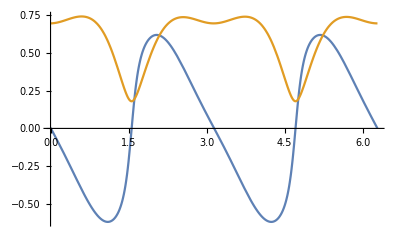

```mathematica
σsol=ListInterpolation[solfin[[2,All,5]],{{0,2π}}];etadeltasol[s_]:=FindRoot[{kinterp[s]^2(Cosh[η]-Sinh[η]Cos[2δ])-etabsol^2,σsol[s]-Sin[2δ]Sinh[η]},{{η,0.1+0.000Cos[NFP s]},{δ,0.1Sin[NFP s]+(NFP s)/2}},MaxIterations->300,AccuracyGoal->4,PrecisionGoal->4,Method->{"AffineCovariantNewton"},DampingFactor->0.1];
etdesol=ParallelTable[etadeltasol[s],{s,0,2π,(2π)/500}];
(*deltaaa=0;etaa=0.7;imax=1000;etdesol=Table[0,{i,1,imax}];For[i=1,i≤ imax,i++,s=(2π i)/imax;etdesol[[i]]= FindRoot[{kinterp[s]^2(Cosh[η]-Sinh[η]Cos[2δ])-etabsol^2,σsol[s]-Sin[2δ]Sinh[η]},{{η,etaa},{δ,deltaaa}},MaxIterations->300,AccuracyGoal->4,PrecisionGoal->4,Method->{"AffineCovariantNewton"},DampingFactor->0.1];{etaa,deltaaa}={η/.etdesol[[i]],δ/.etdesol[[i]]};]*)
ϵsol=ListInterpolation[Tanh[η]/.etdesol,{{0,2π}}];
δsol=ListInterpolation[δ/.etdesol,{{0,2π}}];
psi31sconst=ListInterpolation[solfin[[3,All]],{{0,2π}}];
psi3Funcs=Table[ListInterpolation[solfin[[2,All,i]],{{0,2π}}],{i,1,4}];
Plot[{δsol[x]-NFP x/2,ϵsol[x]},{x,0,2π}]
```

### Table of Cos and Sin coefficients

```mathematica
psi3FuncsCos=1/π ParallelTable[GaussLegendreQuadrature[(psi3Funcs[[j]][x]Cos[NFP ii x])/.x->xx,{xx,0,2π},350,22],{j,1,4},{ii,0,7}];
psi3FuncsSin=1/π ParallelTable[GaussLegendreQuadrature[(psi3Funcs[[j]][x]Sin[NFP ii x])/.x->xx,{xx,0,2π},350,22],{j,1,4},{ii,1,7}];
psi3FuncsCosSinTable={Prepend[psi3FuncsCos[[1,2;;7]],psi3FuncsCos[[1,1]]/2],
Prepend[psi3FuncsSin[[2,1;;7]],0],
Prepend[psi3FuncsCos[[3,2;;8]],psi3FuncsCos[[3,1]]/2],
Prepend[psi3FuncsSin[[4,1;;7]],0]};
mutable={1/(2π)NIntegrate[ϵsol[x],{x,0,2π}],1/π ParallelTable[GaussLegendreQuadrature[(ϵsol[x]Cos[NFP ii x])/.x->xx,{xx,0,2π},350,22],{ii,1,7}]}//Flatten;
deltatable={ -NFP,1/π ParallelTable[GaussLegendreQuadrature[((δsol[x]+(NFP x)/2)Sin[NFP ii x])/.x->xx,{xx,0,2π},350,22],{ii,1,7}]}//Flatten;
```

```mathematica
ArcTanh[mutable]
```

{0.639238,0.307497,-0.098981,0.0437235,-0.0243375,0.0146501,-0.00949416,0.00654047}

### Output to Text File

```mathematica
printv="";
nl="
";
printv=printv<>
"NFP = "<>ToString[NFP]<>nl<>
"RAXIS = "<>ToString[R0];
Do[printv=printv<>" "<>ToString[Chop[eRsol[[i]],10^-5]],{i,1,naxR}];printv=printv<>nl<>"ZAXIS = 0 ";
Do[printv=printv<>" "<>ToString[Chop[eZsol[[i]],10^-5]],{i,1,naxZ}];printv=printv<>nl;
printv=printv<>"mu = "<>StringTrim@StringJoin[" "<>ToString[#]&/@mutable]<>nl<>
"delta = "<>StringTrim@StringJoin[" "<>ToString[#]&/@deltatable]<>nl<>
"iota = "<>ToString[iotasol]<>nl<>
"etabar = "<>ToString[etabsol]<>nl<>
"psi31 = "<>StringTrim@StringJoin[" "<>ToString[#]&/@psi3FuncsCosSinTable[[1]]]<>nl<>
"psi32 = "<>StringTrim@StringJoin[" "<>ToString[#]&/@psi3FuncsCosSinTable[[2]]]<>nl<>
"psi33 = "<>StringTrim@StringJoin[" "<>ToString[#]&/@psi3FuncsCosSinTable[[3]]]<>nl<>
"psi34 = "<>StringTrim@StringJoin[" "<>ToString[#]&/@psi3FuncsCosSinTable[[4]]]<>nl<>
"nNormal = "<>ToString[nNormal]
Export["/Users/rogeriojorge/Dropbox/senac/quasisymmetry/surf_input_QS.txt",printv];
```

NFP = 2
RAXIS = 1 0.09 0.00390896 0.000261123
ZAXIS = 0  0.0805985 0.00390426 0.000289108
mu = 0.56438 0.298159 -0.098659 0.0436956 -0.0243327 0.014649 -0.00949387 0.00654038
delta = -2 -2.70625 -0.74136 -0.810404 -0.404564 -0.46916 -0.280256 -0.327636
iota = -0.134158
etabar = 0.724492
psi31 = 1.31932 -0.108756 -0.251607 0.0632435 -0.0667719 0.0230246 -0.00624189
psi32 = 0 -0.958447 0.197604 -0.126056 0.0651788 -0.0188948 0.00393448 -0.00162677
psi33 = -0.359455 1.18408 -0.633307 0.360653 -0.226511 0.0914455 -0.0316796 0.0109267
psi34 = 0 -1.57133 0.595583 -0.412035 0.23543 -0.0927275 0.0311785 -0.0117239
nNormal = 0

## Plots Solution

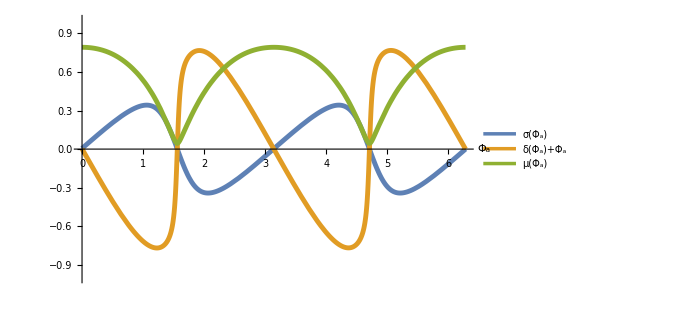

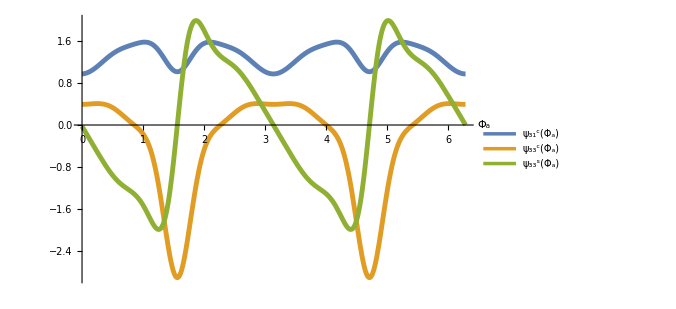

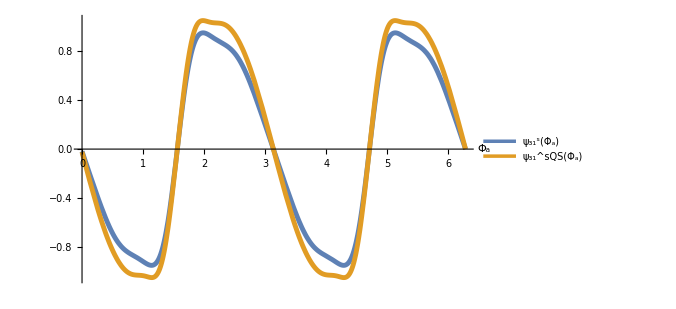

```mathematica
epsdplot=Plot[{σsol[s],δsol[s]-NFP s/2,ϵsol[s]},{s,0,2π},AxesLabel->{Style["Φ_a",Bold,29,FontFamily->"Latin Modern Roman"],Style["",Bold,16]},PlotLabel->"",LabelStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->19],PlotStyle->Thickness[0.007],PlotRange->{Automatic,{-1,1}},Frame->False,ImageSize->500,PlotLegends->{"σ(Φ_a)","δ(Φ_a)+Φ_a","μ(Φ_a)"},AxesOrigin->{0,0}]
psi3dplot=Plot[{psi3Funcs[[1]][s],psi3Funcs[[3]][s],psi3Funcs[[4]][s]},{s,0,2π},PlotRange->All,AxesLabel->{Style["Φ_a",Bold,29,FontFamily->"Latin Modern Roman"],Style["",Bold,16]},PlotLabel->"",LabelStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->19],PlotStyle->Thickness[0.007],Frame->False,ImageSize->500,PlotLegends->{"ψ_31^c(Φ_a)","ψ_33^c(Φ_a)","ψ_33^s(Φ_a)"},AxesOrigin->{0,0}]
psi31sdplot=Plot[{psi3Funcs[[2]][s],psi3Funcs[[2]][s]-psi31sconst[s]},{s,0,2π},PlotRange->All,AxesLabel->{Style["Φ_a",Bold,29,FontFamily->"Latin Modern Roman"],Style["",Bold,16]},PlotLabel->"",LabelStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->19],PlotStyle->Thickness[0.007],Frame->False,ImageSize->500,PlotLegends->{"ψ_31^s(Φ_a)","ψ_31^sQS(Φ_a)"},AxesOrigin->{0,0}]
Export["/Users/rogeriojorge/Dropbox/senac/quasisymmetry/epsdplot_NFP"<>ToString[NFP]<>".pdf",epsdplot];
Export["/Users/rogeriojorge/Dropbox/senac/quasisymmetry/psi3dplot_NFP"<>ToString[NFP]<>".pdf",psi3dplot];
Export["/Users/rogeriojorge/Dropbox/senac/quasisymmetry/psi31sdplot_NFP"<>ToString[NFP]<>".pdf",psi31sdplot];
```